```mathematica
Manipulate[
Module[
{sol=NDSolve[
{x'[t]==k*x[t-τ],x[t/;t<=0]==1},
x,{t,-5,10*τ}]
},
Plot[Evaluate[x[t]/.sol],{t,-2,10*τ}]
],
{k,-2,2},
{τ, 0, 4}
]
```

-1.7

{{x→InterpolatingFunction[…]}}

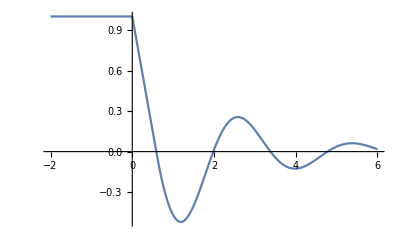

```mathematica
τ:=0.6
k=-1.7
sol=NDSolve[
{x'[t]==k*x[t-τ],x[t/;t<=0]==1},
x,{t,-5,10*τ}]

Plot[Evaluate[x[t]/.sol],{t,-2,10*τ}]
```

```mathematica
Manipulate[
ComplexPlot3D[
-ProductLog[τ*z]/τ, {z,-1-1I, 1 + 1I}
],
{τ,1,10}
]
```

```mathematica
Manipulate[
Module[
{sol=NDSolve[
{x'[t]==r*x[t]*(1-x[t-τ]/K),x[t/;t<=0]==1},
x,{t,-5,10*τ}]
},
Plot[Evaluate[x[t]/.sol],{t,-2,10*τ}]
],
{r,-2,2},
{K,1,2},
{τ, 1, 4}
]
```

```mathematica
Manipulate[
Module[
{sol=NDSolve[
{x'[t]==x[t]-x[t]^3-α*x[t-τ],x[t/;t<=0]==1},
x,{t,-1,20*τ}]
},
Plot[Evaluate[x[t]/.sol],{t,-1,20*τ}]
],
{α,-1,1},
{τ, 1, 8}
]
```

```mathematica
Plot[{ProductLog[-1,x],ProductLog[x]},{x,-2,5}, PlotRange->{-6,2}, PlotLabels->"Expressions", Epilog->{
Dashed,Line[{{-1/E, 2}, {-1/E, -6}}]
}]
```

-Graphics-

```mathematica
Clear[r,τ]
Solve[l==r*Exp[-l*τ],l]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{l→ProductLog[r τ]/τ}}

```mathematica
First[{{l->1/2 ProductLog[2 r]}}]
```

{l→1/2 ProductLog[2 r]}

```mathematica
l/.{l->1/2 ProductLog[2 r]}
```

```mathematica
Manipulate[
ComplexPlot3D[1/τ ProductLog[2τ*r],{r,-5-5I,5+5I}, PlotRange->{-5,5}],
{τ,1,5}
]
```

```mathematica
Exp[-b*τ*I]
```

ⅇ^(-ⅈ b τ)

```mathematica
ExpToTrig[ⅇ^(-ⅈ b τ)]
```